```mathematica
(* "C:\\Path\\to\\the\\mathematica\\function\\files" *)
AppendTo[$Path,"C:\\Users\\Documents\\Functions"];
```

```mathematica
<<GeneralFunctions.m
<<QuantityFunctions.m
<<OpticsFunctions.m
```

### Gaussian Resonator

#### Display

```mathematica
RadioButtonBar[Dynamic[method1],{"Generate","Load"}]
```

| Generate   | Load

```mathematica
Switch[method1,
"Generate",
qz0dPowerDict11=getCycleData[f11];
qz0dPowerDict18=getCycleData[f18];,
"Load",
qz0dPowerDict11=Import["qz0dPowerDict11.mx"];
qz0dPowerDict18=Import["qz0dPowerDict18.mx"];
]
(*Default values: "cycles" -> 20,"MFD" ->μmQ[mfd830//First],"PosColimnatingLens"->-1270Quantity[, "Millimeters"],"initialOffset"->0Quantity[, "Millimeters"],"wavelength"->nmQ[780],"iof" -> 1,"focalLength" -> 1Quantity[, "Meters"] ,"aperturePC" -> 2Quantity[, "Millimeters"]/2,"maxL" ->5000Quantity[, "Millimeters"] ,"Δmax" ->200 Quantity[, "Millimeters"],"Δmin" ->25 Quantity[, "Millimeters"], "InitialPower"->1*)
```

```mathematica
RadioButtonBar[Dynamic[method2],{"Generate","Load"}]
```

| Generate   | Load

```mathematica
Switch[method2,
"Generate",
{minCouplingData11,exitingBeamsData11}=getCouplingData[f11,qz0dPowerDict11];
{minCouplingData18,exitingBeamsData18}=getCouplingData[f18,qz0dPowerDict18];,
"Load",
minCouplingData11=Import["minCouplingData11.mx"];
exitingBeamsData11=Import["exitingBeamsData11.mx"];
minCouplingData18=Import["minCouplingData18.mx"];
exitingBeamsData18=Import["exitingBeamsData18.mx"];
]
(*Default options for getCouplingData: "cycles" -> 20,"MFD" ->μmQ[5.8],"PosColimnatingLens"->-1270Quantity[, "Millimeters"],"initialOffset"->0Quantity[, "Millimeters"],"wavelength"->nmQ[780],"iof" -> 1,"focalLength" -> 1Quantity[, "Meters"] ,"aperturePC" -> 2Quantity[, "Millimeters"]/2,"lensRadius"->2.75Quantity[, "Millimeters"]*)
```

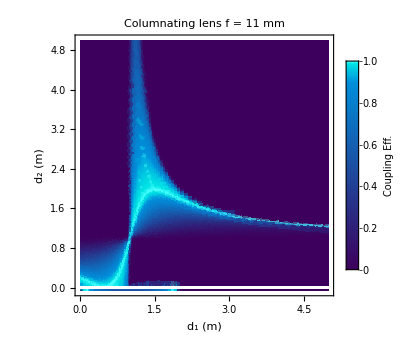
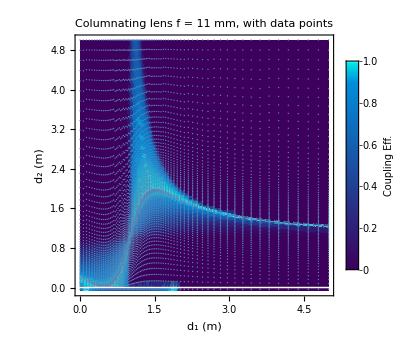
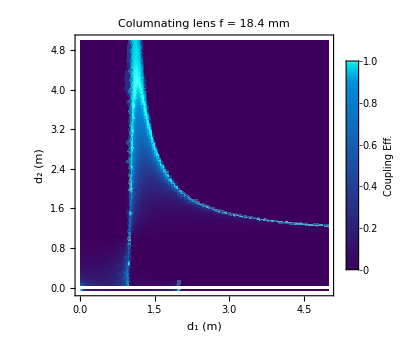
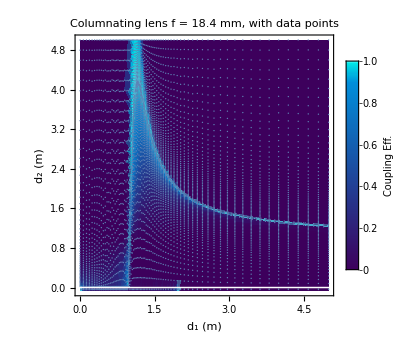
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[{
{plotCouplingData[minCouplingData11,showDataPoints->False,PlotLabel->"Columnating lens f = 11 mm"],
plotCouplingData[minCouplingData11,PlotLabel->"Columnating lens f = 11 mm, with data points"]},
{plotCouplingData[minCouplingData18,showDataPoints->False,PlotLabel->"Columnating lens f = 18.4 mm"],
plotCouplingData[minCouplingData18,PlotLabel->"Columnating lens f = 18.4 mm, with data points"]}},Spacings->2]
```

```mathematica
beamDataPlots={};
For[i=1,i<=Length[exitingBeamsData11],i++,
AppendTo[beamDataPlots,
plotCouplingData[{#[[1]],#[[2]],Min[#[[3]],#[[4]]]}&/@exitingBeamsData11[[i]],showDataPoints->False,PlotLabel->sf["After `` Cycles, Columnating lens f = 11 mm",i]]
];
]
```

```mathematica
Manipulate[Show[beamDataPlots[[n]]],{n,1,Length[beamDataPlots],1,Appearance->"Open"},ControlPlacement->Top ]
```

```mathematica
(*
"Exact" uses the values given;
"Nearest" uses the data of the closest point in the given database (e.g. minCouplingData11);
"Solution1" uses the solution for the simpler case with only one distanst (Subscript[d, 1]) for both Subscript[d, 1] and Subscript[d, 2];
"Solution2" uses the point along the solution where Subscript[d, 1] is the given value;

fillType,
"power" Opacity = the remaining power of the beam;
"constant" Opacity = 0.05 (Best for seeing multiple cycles on the same plot);
"gaussian" Opacity = Gaussian dist. of power where ~86.5% of remaining power is within the width(calculation takes more time);
"log" Opacity = Log of the Gaussian to imitate what our eyes would see (calculation takes more time);

clipBeam restricts the width to the radius of the most recent component 
*)
plts1=getBeamPlots[f11,2010,2020,"Exact","fillType"->"power","database"->Null,"clipBeam"->True,"initialOffset"->0 Quantity[, "Millimeters"]];
plts2=getBeamPlots[f11,2010,2020,"Exact","fillType"->"constant","database"->Null,"clipBeam"->False];
plts3=getBeamPlots[f11,2010,2020,"Exact","fillType"->"gaussian","database"->Null,"clipBeam"->True];
plts4=getBeamPlots[f11,2010,2020,"Exact","fillType"->"log","database"->Null,"clipBeam"->True];
```

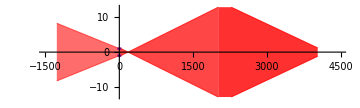
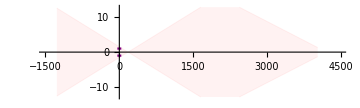
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Show[plts1[[12]],ImageSize->Medium],Show[plts2[[12]],ImageSize->Medium],
Show[plts3[[12]],ImageSize->Medium],Show[plts4[[12]],ImageSize->Medium]}
```

```mathematica
Manipulate[If[overlay,
Show[plts4[[;;Round[2 n]]]],
Show[plts4[[Round[2 n]]]]
],{{overlay,True,"Overlay"},{True->"On",False->"Off"},ControlType->RadioButtonBar},{{n,0.5,"Cycle"},0.5,Length[plts4]/2,0.5,Appearance->"Open"},ControlPlacement->Top ]
```

#### Initial Calculations

-Graphics-

-Graphics-

↑ from ThorLabs

```mathematica
(* mode field diameter (MFD) 
used for calculating acceptance angle of SM fibers *)
(*μm @ 850 nm for SM 780*)
mfd780=Around[5.0,0.5];
(*μm @ 830 nm for SM 830*)
mfd830=Around[5.8,1.1];
```

```mathematica
λ0=780//nmQ; (* wavelength of the light *)
f18=18.4//mmQ; (* focal length of columnating lens *)
f11=11//mmQ; (* focal length of another columnating lens *)
zi=-1270//mmQ; (* position of columnating lens *)
focalLength = 1//mQ; (* focal length of the mirror *)
f=mmMag[focalLength];
```

```mathematica
qFreeSpace[qLens[qFreeSpace[qq,md1],fL],md1];
genSolution1=SolveValues[%==qq,{md1}]//Flatten
qFreeSpace[qLens[qFreeSpace[qLens[qFreeSpace[qq,md1],fL],2 md2],fL],md1];
genSolution2=SolveValues[%==qq,{md2}][[1,1]]
```

{fL-√(fL^2+qq^2),fL+√(fL^2+qq^2)}

(-fL^2 md1+fL md1^2-fL qq^2)/(fL^2-2 fL md1+md1^2-qq^2)

#### Main Calculations

```mathematica
getCycleData[focusColimnatingLens_,
opts:OptionsPattern[{"cycles" -> 20,"MFD" ->μmQ[mfd830//First],"PosColimnatingLens"->-1270 Quantity[, "Millimeters"],"initialOffset"->0 Quantity[, "Millimeters"],"wavelength"->nmQ[780],"iof" -> 1,"focalLength" -> 1 Quantity[, "Meters"] ,"aperturePC" -> 2 Quantity[, "Millimeters"]/2,"maxL" ->5000 Quantity[, "Millimeters"] ,"Δmax" ->200 Quantity[, "Millimeters"],"Δmin" ->25 Quantity[, "Millimeters"],"InitialPower"->1,"StartComp"->2}]]:=
Module[{qz0dPowerDict=<||>,q00,d00,f0=mmMag[focusColimnatingLens],q,z0,cycles,MFDmm,zi,offset,λmm,iof,f,aPC,maxL,Δmax,Δmin,start,power,sol1,sol2,components,mirror1,mirror2},

cycles=OptionValue["cycles"];
MFDmm=OptionValue["MFD"]//mmMag;
zi=OptionValue["PosColimnatingLens"]//mmMag;
offset=OptionValue["initialOffset"]//mmMag;
λmm=OptionValue["wavelength"]//mmMag;
iof=OptionValue["iof"];
f=OptionValue["focalLength"]//mmMag;
aPC=OptionValue["aperturePC"]//mmMag;
maxL=OptionValue["maxL"]//mmMag;
Δmax=OptionValue["Δmax"]//mmMag;
Δmin=OptionValue["Δmin"]//mmMag;
power=OptionValue["InitialPower"];
start=OptionValue["StartComp"];

q00=0+ⅈ zr/.{mfd->MFDmm,λ->λmm};
d00=Last[Values@FindRoot[Re[qLens[qFreeSpace[q00,x],f0]]==zi+offset,{x,1.1f0}]];

{q,z0}=qz0ToNextComp[q00,zi-d00,zi,f0];

sol1=Re[genSolution1/.{qq->q-zi,fL->f}];
sol2[md_]:=Re[genSolution2/.{qq->q-zi,fL->f,md1->md}];

Monitor[
Do[
AppendTo[qz0dPowerDict,md1-><||>];
Do[
mirror1 = md1; 
mirror2 = md2;

components={{0,∞,aPC},
{md1,f,12.7},
{(md2+md1),∞,12.7/2}};

If[Chop[md2]==0,
components=Most[components];
];

AppendTo[qz0dPowerDict[md1],md2->qz0dCyclePower[q,z0,components,cycles,"wavelength"->λmm,"InitialPower"->power,"Start"->start]];

,{md2,NormDistList[0,maxL,sol2[md1],Δmax,Δmin]}]
,{md1,NormDistList[0,maxL,1000,Δmax,Δmin]}];

Do[
If[MissingQ[qz0dPowerDict[md1]],
AppendTo[qz0dPowerDict,md1-><||>];
Do[
If[md2<0,Continue[]];
mirror1 = md1; 
mirror2 = md2;

components={{0,∞,aPC},
{md1,f,12.7},
{(md2+md1),∞,12.7/2}};

If[Chop[md2]==0,
components=Most[components];
];

AppendTo[qz0dPowerDict[md1],md2->qz0dCyclePower[q,z0,components,cycles,"wavelength"->λmm,"InitialPower"->power,"Start"->start]];

,{md2,Max[sol2[md1],0]+{0,-Δmin,+Δmin}}]
];
,{md1,NormDistList[0,maxL,1000,Δmax/2,Δmin/2]}];

Do[
If[MissingQ[qz0dPowerDict[md1]],
AppendTo[qz0dPowerDict,md1-><||>];
Do[
mirror1 = md1; 
mirror2 = md2;

components={{0,∞,aPC},
{md1,f,12.7},
{(md2+md1),∞,12.7/2}};

If[Chop[md2]==0,
components=Most[components];
];

AppendTo[qz0dPowerDict[md1],md2->qz0dCyclePower[q,z0,components,cycles,"wavelength"->λmm,"InitialPower"->power,"Start"->start]];

,{md2,{0}}]
];
,{md1,sol1}];
,Row[{"Current: d_1 = ",mirror1," mm, d_2 = ",mirror2," mm"}]];

qz0dPowerDict
]
```

```mathematica
qz0dPowerDict11=getCycleData[f11];
```

```mathematica
qz0dPowerDict18=getCycleData[f18];
```

```mathematica
Total[Length[#]&/@qz0dPowerDict11]
Total[Length[#]&/@qz0dPowerDict18]
```

5829

5101

```mathematica
Export["qz0dPowerDict11.mx",qz0dPowerDict11]
```

qz0dPowerDict11.mx

```mathematica
Export["qz0dPowerDict18.mx",qz0dPowerDict18]
```

qz0dPowerDict18.mx

#### Plotting beam widths throughout storage

```mathematica
Clear[getBeamPlots];

getBeamPlots[focusColimnatingLens_,d1_,d2_,method_:"Exact",
opts:OptionsPattern[{"fillType"->"power","database"->Null,"cycles" -> 20,"clipBeam"->True,"MFD" ->μmQ[mfd830//First],"PosColimnatingLens"->-1270 Quantity[, "Millimeters"],"initialOffset"->0 Quantity[, "Millimeters"],"wavelength"->nmQ[780],"iof" -> 1,"focalLength" -> 1 Quantity[, "Meters"] ,"aperturePC" -> 2 Quantity[, "Millimeters"]/2,"InitialPower"->1,"StartComp"->2}]]:=
Module[{qz0Values,fillType,showPower,constantPower,showLog,database,dm1,dm2,q00,d00,f0=mmMag[focusColimnatingLens],q,z0,cycles,clipBeam,MFDmm,zi,offset,λmm,iof,f,aPC,start,power,sol1,sol2,components,plts,aspectR,dmax,curveFix,curveFixLens,lensThickness,vals1,vals2,i,maxIndex,pltRange,isExiting,frac1,frac2,fracOut,wz1,wz2,rnge1,rnge2,rngeOut,power1,power2,powerOut,thickness=40,gaussianOpacity1,gaussianOpacity2,logPerceivedOpacity1,logPerceivedOpacity2},

fillType=OptionValue["fillType"];
database=OptionValue["database"];
cycles=OptionValue["cycles"];
clipBeam=OptionValue["clipBeam"];
MFDmm=OptionValue["MFD"]//mmMag;
zi=OptionValue["PosColimnatingLens"]//mmMag;
offset=OptionValue["initialOffset"]//mmMag;
λmm=OptionValue["wavelength"]//mmMag;
iof=OptionValue["iof"];
f=OptionValue["focalLength"]//mmMag;
aPC=OptionValue["aperturePC"]//mmMag;
power=OptionValue["InitialPower"];
start=OptionValue["StartComp"];

Switch[fillType,
"power",
showPower=True;
constantPower=False,

"constant",
showPower=True;
constantPower=True,

"gaussian",
showPower=False;
showLog=False,

"log",
showPower=False;
showLog=True,

_,(*default*)
Print["Invalid \"fillType\".\n
Options include: \"power\", \"constant\", \"gaussian\", and \"log\".\n
\"fillType\"->\"power\" used by default"];
showPower=True
];


q00=0+ⅈ zr/.{mfd->MFDmm,λ->λmm};
d00=Last[Values@FindRoot[Re[qLens[qFreeSpace[q00,x],f0]]==zi+offset,{x,1.1f0}]];

{q,z0}=qz0ToNextComp[q00,zi-d00,zi,f0];

sol1=Re[genSolution1/.{qq->q-zi,fL->f}];
sol2[md_]:=Re[genSolution2/.{qq->q-zi,fL->f,md1->md}];

Switch[method,
"Nearest",
{dm1,dm2}=Nearest[getKeyPaths[database],{d1,d2}]//First;
qz0Values=database[dm1,dm2],

"Solution1",
{dm1,dm2}={Last[sol1,sol1],sol2[Last[sol1,sol1]]},

"Solution2",
{dm1,dm2}={d1,sol2[d1]},

"Exact",
{dm1,dm2}={d1,d2},

_,(*default*)
Print["Invalid method.\n
Options include: \"Nearest\", \"Solution1\", \"Solution2\", and \"Exact\".\n
method = \"Exact\" used by default"];
{dm1,dm2}={d1,d2}
];

If[!ValueQ[qz0Values],
components={{0,∞,aPC},
{dm1,f,12.7},
{(dm2+dm1),∞,12.7/2}};
If[Chop[dm2]==0,
components=Most[components];
];

qz0Values=qz0dCyclePower[q,z0,components,cycles,"wavelength"->λmm];
];


plts={};
aspectR=0.3;
dmax=Max[dm1+dm2+40,2f];
pltRange={{-1500,1.1dmax},{-12.7,12.7}};
curveFix=aspectR(pltRange[[1,2]] -pltRange[[1,1]])/(pltRange[[2,2]] -pltRange[[2,1]]);

curveFixLens=aspectR(1.1 2f+1500)/(2 12.7);

lensThickness=setSigFigs[
Quiet@SolveValues[Δx==2f(1-Cos[θ])&&
Sin[θ]==12.7*curveFixLens/(2f)&&
0<θ<=π/4,{Δx,θ}][[1,1]],
3,True];

If[!ValueQ[lensGraphic],
lensGraphic=RegionPlot[-12.7<=y<=12.7&&
2f>=Norm[{x+2f-lensThickness,y*curveFixLens}]&&
2f>=Norm[{x-2f+lensThickness,y*curveFixLens}],
{x,0-lensThickness,0+lensThickness},
{y,pltRange[[2,1]],pltRange[[2,2]]},
BoundaryStyle->Thin,
PlotRange->{1.1{-lensThickness,lensThickness},1.01{pltRange[[2,1]],pltRange[[2,2]]}},
AspectRatio->Full,MaxRecursion->2,Mesh->None,Frame->False];
];

If[!ValueQ[pcGraphics],
pcGraphics=Plot[{mmMag[aPC],-mmMag[aPC]},{z,-80/2,80/2},PlotStyle->Directive[Purple](*,
PlotLabels->Placed[{"PC aperture",""},{{Scaled[1.5],Before}}]*)];
];

If[!ValueQ[flatMirrorGraphic],
flatMirrorGraphic=RegionPlot[-12.7/2<=y<=12.7/2&&0<=x<=thickness,
{x,0,thickness},
{y,pltRange[[2,1]],pltRange[[2,2]]},
PlotRange->{{-0.1thickness,1.1thickness},1.01{pltRange[[2,1]],pltRange[[2,2]]}},
AspectRatio->Full,MaxRecursion->2,Mesh->None,Frame->False];
];

maxIndex=Length[qz0Values];
(*maxIndex=4;*)

rnge2={dm1,dm1+dm2};
rngeOut={mmMag[zi],0};

Monitor[
For[i=1,i<maxIndex,i+=2,
rnge1={0,dm1};

If[Sign[Im[qz0Values[[i]][[1]]]]==1,
vals1=qz0Values[[i]];
vals2=qz0Values[[i+1]];
isExiting=False;
,
vals1=qz0Values[[i+1]];
vals2=qz0Values[[i]];
isExiting=True;
];

wz1[z_]:=wz[z,vals1[[2]],λmm,Im[vals1[[1]]],iof];
power1=vals1[[3]];
frac1=vals1[[4]];
wz2[z_]:=wz[z,vals2[[2]],λmm,Im[vals2[[1]]],iof];
power2=vals2[[3]];
frac2=vals2[[4]];

If[i==1,
rnge1={mmMag[zi],dm1};
];


If[isExiting,
powerOut = 
Min[power1,powerThrough[aPC,wz[0,vals1[[2]],λmm,Im[vals1[[1]]],iof]]];
fracOut=
Min[frac1,aPC/wz[0,vals1[[2]],λmm,Im[vals1[[1]]],iof]];
];

If[!clipBeam,
frac1=1;
frac2=1;
fracOut=1;
];

If[constantPower,
power1=0.05;
power2=0.05;
powerOut=0.05;
];

If[!showPower,
gaussianOpacity1[z_,y_]=0.7227897522452308/wz1[z](ⅇ^(-2 (y/wz1[z])^2))//N;
gaussianOpacity2[z_,y_]=0.7227897522452308/wz2[z](ⅇ^(-2 (y/wz2[z])^2))//N;
If[showLog,
logPerceivedOpacity1[z_,y_,k_:5]=
Log[1+k gaussianOpacity1[z,y]]/Log[1+k]//N;
logPerceivedOpacity2[z_,y_,k_:5]=
Log[1+k gaussianOpacity2[z,y]]/Log[1+k]//N
,
logPerceivedOpacity1[z_,y_]=gaussianOpacity1[z,y];
logPerceivedOpacity2[z_,y_]= gaussianOpacity2[z,y]
];

AppendTo[plts,
Show[
RegionPlot[Abs[y]<=frac1 wz1[z]&&rnge1[[1]]<=z<=rnge1[[2]],
{z,rnge1[[1]],rnge1[[2]]},
{y,pltRange[[2,1]],pltRange[[2,2]]},
PlotRange->pltRange,
BoundaryStyle->None,
ColorFunction->Function[{z,y},
Directive[Red,Opacity[logPerceivedOpacity1[z,y]]]
],ColorFunctionScaling->False,
ImageSize->Full,AspectRatio->aspectR,
PlotPoints->25,MaxRecursion->4,Mesh->None,
Epilog->{
Inset[lensGraphic,{dm1,0},{0,0},{2lensThickness,pltRange[[2,2]]-pltRange[[2,1]]}],
Inset[lensGraphic,{mmMag[zi],0},{0,0},{50,4}],Inset[flatMirrorGraphic,{dm1+dm2,0},{0,0},{thickness,pltRange[[2,2]]-pltRange[[2,1]]}]
}
],
RegionPlot[Abs[y]<=frac2 wz2[z]&&rnge2[[1]]<=z<=rnge2[[2]],
{z,rnge2[[1]],rnge2[[2]]},
{y,pltRange[[2,1]],pltRange[[2,2]]},
PlotRange->pltRange,
BoundaryStyle->None,
ColorFunction->Function[{z,y},
Directive[Red,Opacity[logPerceivedOpacity2[z,y]]]
],ColorFunctionScaling->False,
ImageSize->Full,AspectRatio->aspectR,
PlotPoints->25,MaxRecursion->4,Mesh->None]
,
If[isExiting,
RegionPlot[Abs[y]<=fracOut wz1[z]&&rngeOut[[1]]<=z<=rngeOut[[2]],
{z,rngeOut[[1]],rngeOut[[2]]},
{y,pltRange[[2,1]],pltRange[[2,2]]},
PlotRange->pltRange,
BoundaryStyle->None,
ColorFunction->Function[{z,y},
Directive[Red,Opacity[logPerceivedOpacity1[z,y]]]
],ColorFunctionScaling->False,
ImageSize->Full,AspectRatio->aspectR,
PlotPoints->25,MaxRecursion->4,Mesh->None],
{}]
,
pcGraphics]
];
,
AppendTo[plts,
Show[
Plot[{frac1 wz1[z],-frac1 wz1[z]},{z,rnge1[[1]],rnge1[[2]]},
PlotStyle->Directive[Red,Thickness[0.002],Opacity[power1]],
PlotRange->pltRange,Filling->{1->{2}},FillingStyle->Directive[Red,Opacity[power1]],
ImageSize->Full,AspectRatio->.3,
Epilog->{
Inset[lensGraphic,{dm1,0},{0,0},{2lensThickness,pltRange[[2,2]]-pltRange[[2,1]]}],
Inset[lensGraphic,{mmMag[zi],0},{0,0},{50,4}],Inset[flatMirrorGraphic,{dm1+dm2,0},{0,0},{thickness,pltRange[[2,2]]-pltRange[[2,1]]}]
}
],
Plot[{frac2 wz2[z],-frac2 wz2[z]},{z,rnge2[[1]],rnge2[[2]]},
PlotStyle->Directive[Red,Thickness[0.002],Opacity[power2]],
PlotRange->pltRange,Filling->{1->{2}},FillingStyle->Directive[Red,Opacity[power2]],
ImageSize->Full,AspectRatio->.3]
,
If[isExiting,
Plot[{fracOut wz1[z],-fracOut wz1[z]},{z,rngeOut[[1]],rngeOut[[2]]},
PlotStyle->Directive[Red,Thickness[0.002],Opacity[powerOut]],
PlotRange->pltRange,Filling->{1->{2}},FillingStyle->Directive[Red,Opacity[powerOut]],
ImageSize->Full,AspectRatio->.3],
{}]
,
pcGraphics]
];
]
]
,Row[{"d_1 = ",dm1," mm, d_2 = ",dm2," mm   ",Round[i/maxIndex 100,0.1],"%"}]];
plts
]
```

```mathematica
qz0dPowerDict11
```

```mathematica
plts1=getBeamPlots[f11,2010,2020,"Exact","fillType"->"power","database"->Null,"clipBeam"->True,"initialOffset"->0 Quantity[, "Millimeters"]];
```

```mathematica
Manipulate[If[overlay,
Show[plts1[[;;Round[2 n]]]],
Show[plts1[[Round[2 n]]]]
],{{overlay,True,"Overlay"},{True->"On",False->"Off"},ControlType->RadioButtonBar},{{n,0.5,"Cycle"},0.5,Length[plts1]/2,0.5,Appearance->"Open"},ControlPlacement->Top ]
```

#### Post Calculations

```mathematica
getCouplingData//ClearAll;

getCouplingData[focusColimnatingLens_,database_,opts:OptionsPattern[{"cycles" -> 20,"MFD" ->μmQ[5.8],"PosColimnatingLens"->-1270 Quantity[, "Millimeters"],"initialOffset"->0 Quantity[, "Millimeters"],"wavelength"->nmQ[780],"iof" -> 1,"focalLength" -> 1 Quantity[, "Meters"] ,"aperturePC" -> 2 Quantity[, "Millimeters"]/2,"lensRadius"->2.75 Quantity[, "Millimeters"],"StartComp"->2}]]:=
Module[{minCouplingData={},exitingBeamsData={},exitingBeams,d00,f0=mmMag[focusColimnatingLens],q,z0,cycles,MFDmm,zi,λmm,iof,f,aPC,start,correctPower=1./powerThrough[1,1]},

cycles=OptionValue["cycles"];
MFDmm=OptionValue["MFD"]//mmMag;
zi=OptionValue["PosColimnatingLens"]//mmMag;
offset=OptionValue["initialOffset"]//mmMag;
λmm=OptionValue["wavelength"]//mmMag;
iof=OptionValue["iof"];
f=OptionValue["focalLength"]//mmMag;
aPC=OptionValue["aperturePC"]//mmMag;
lensRadius=OptionValue["lensRadius"]//mmMag;
start=OptionValue["StartComp"];

q00=0+ⅈ zr/.{mfd->MFDmm,λ->λmm};
d00=Last[Values@FindRoot[Re[qLens[qFreeSpace[q00,x],f0]]==zi+offset,{x,1.1f0}]];

smfRmm=MFDmm/2;

Monitor[
Do[
dm1=md1;
Do[
dm2=md2;
exitingBeams=Select[database[md1,md2],Chop[Re[#[[1]]]+#[[2]]-md1]==0&&Im[#[[1]]]<0&];

If[Length[exitingBeams]==0,Continue[]];

exitingBeams=qz0ToNextComp[#[[1]],#[[2]],zi,f0]~Join~{Quiet[Min[#[[3]],
powerThrough[aPC,wz[0,#[[2]],λmm,Im[#[[1]]],iof]],powerThrough[lensRadius,wz[zi,#[[2]],λmm,Im[#[[1]]],iof]]],
General::munfl]}&/@exitingBeams;

exitingBeams={md1/1000,md2/1000,#[[3]],
Quiet[Min[1,
correctPower*powerThrough[smfRmm,wz[zi-d00,#[[2]],λmm,Im[#[[1]]],iof]]],
General::munfl]}&/@exitingBeams;

minPowerCoupled=Min[Min[#[[3]],#[[4]]]&/@exitingBeams];

AppendTo[minCouplingData,{md1/1000,md2/1000,minPowerCoupled}];

If[Length[exitingBeams]<cycles,
For[j=Length[exitingBeams]+1,j<=cycles,j++,
AppendTo[exitingBeams,{md1/1000,md2/1000,0,0}]
]
];

AppendTo[exitingBeamsData,exitingBeams];

,{md2,database[md1]//Keys}]
,{md1,database//Keys}]
,Row[{"d_1 = ",dm1," mm, d_2 = ",dm2," mm"}]];

{minCouplingData,Transpose[exitingBeamsData,1<->2]}
]
```

```mathematica
{minCouplingData11,exitingBeamsData11}=getCouplingData[f11,qz0dPowerDict11];
{minCouplingData18,exitingBeamsData18}=getCouplingData[f18,qz0dPowerDict18];
```

```mathematica
Export["minCouplingData11.mx",minCouplingData11];
Export["exitingBeamsData11.mx",exitingBeamsData11];
Export["minCouplingData18.mx",minCouplingData18];
Export["exitingBeamsData18.mx",exitingBeamsData18];
```

```mathematica
ClearAll[plotCouplingData]
Options[plotCouplingData]=Join[{"showDataPoints"->True,"showRow0"->True},Options[ListDensityPlot]];

plotCouplingData[data_,opts:OptionsPattern[]]:=Module[{showDataPoints,showRow0,densityOpts,densityPlot,overlay,densityPlot0,overlay0,extraRow0={},getOptionOrDefault,colorFunc,blendList,plotLegends},

(*Extract custom options*)
showDataPoints=OptionValue["showDataPoints"];
showRow0=OptionValue["showRow0"];

(*Extract ListDensityPlot options*)
densityOpts=FilterRules[FilterRules[
{opts},Options[ListDensityPlot]],
Except[{ColorFunction,PlotLegends,ImageSize,AxesLabel,InterpolationOrder,PlotRange}]];


blendList=
{{0,Blend[{Darker[Blue,.4],Darker[Purple,.4]},.8]},
{.9,Blend[{Darker[Cyan,.2],Blue},.3]},
{.99,Darker[Cyan,.1]},
{1,Lighter[Cyan,.3]}};
colorFunc=
Blend[blendList,#]&;

plotLegends=Column[{
BarLegend[{colorFunc,{0,1}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Coupling Eff.",LabelStyle->{FontFamily->"Helvetica"}](*,
LineLegend[{Lighter[Blue,.9]},{"Solution"}]*)}];

getOptionOrDefault[sym_,fallback_]:=If[KeyExistsQ[Association[opts],sym],OptionValue[sym],fallback];

densityOpts=densityOpts~Join~
{ColorFunction->getOptionOrDefault[ColorFunction,colorFunc],
PlotLegends->getOptionOrDefault[PlotLegends,plotLegends],
ImageSize->getOptionOrDefault[ImageSize,350],
AxesLabel->getOptionOrDefault[AxesLabel,{"d_1 (m)","d_2 (m)"}],
InterpolationOrder->getOptionOrDefault[InterpolationOrder,2],
PlotRange->getOptionOrDefault[PlotRange,{0,1}]
};

Do[
If[Chop[1000p[[2]]]!=0,Continue[],
AppendTo[extraRow0,{p[[1]],0,p[[3]]}];
AppendTo[extraRow0,{p[[1]],-35/1000,p[[3]]}];
AppendTo[extraRow0,{p[[1]],-60/1000,p[[3]]}];
];
,{p,data}
];

densityPlot=
ListDensityPlot[{data,If[showRow0,extraRow0,Nothing]},Evaluate[densityOpts]];

overlay=If[showDataPoints,
ListPlot[
Tooltip[{#[[1]],#[[2]]},
Row[{
Quiet@setSigFigs[#[[3]],3],
" (",1000#[[1]]," mm, ",Max[1000#[[2]],0]," mm)"
}],
TooltipStyle->{Background->White,CellFrameColor->Automatic}
]&/@data~Join~If[showRow0,Select[extraRow0,#[[2]]==-35/1000&],{}]],
Nothing
];

Show[{densityPlot,overlay,If[showRow0,Graphics[{White,Rectangle[{-0.5,-0.01},{10,0.02}]}],Nothing]}]
]
```

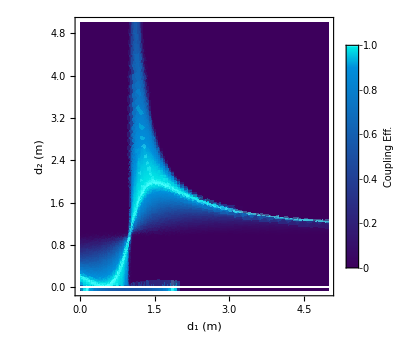

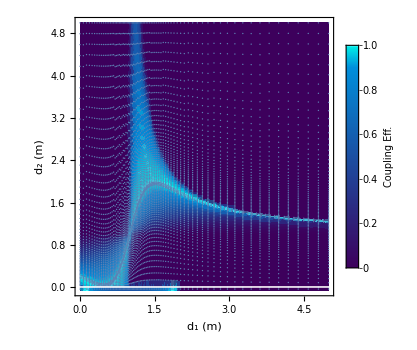

```mathematica
plotCouplingData[minCouplingData11,"showDataPoints"->False]
plotCouplingData[minCouplingData11]
```

```mathematica
blendList4=
{{0,Blend[{Darker[Blue,.4],Darker[Purple,.4]},.8]},
{.6,Blend[{Darker[Cyan,.4],Darker[Purple,.2]},.6]},
{.9,Blend[{Darker[Cyan,.4],Darker[Blue,.2]},.3]},
{1,Darker[Cyan,.2]}}
colorFunc4=Blend[blendList4,#]&;
legendList4={6(#[[1]]-1),#[[2]]}&/@blendList4
BarLegend[{colorFunc4,{0,1}},LegendLayout->"Row"]
```

{{0,RGBColor[0.24, 0., 0.36]},{0.6,RGBColor[0.24, 0.24, 0.48]},{0.9,RGBColor[0., 0.42, 0.66]},{1,RGBColor[0., 0.8, 0.8]}}

{{-6,RGBColor[0.24, 0., 0.36]},{-2.4,RGBColor[0.24, 0.24, 0.48]},{-0.6,RGBColor[0., 0.42, 0.66]},{0,RGBColor[0., 0.8, 0.8]}}

```mathematica
blendList8=
{{0,Blend[{Darker[Blue,.4],Darker[Purple,.4]},.8]},
{.9,Blend[{Darker[Cyan,.2],Blue},.3]},
{.99,Darker[Cyan,.1]},{1,Lighter[Cyan,.3]}}
colorFunc8=Blend[blendList8,#]&;
legendList8={6(#[[1]]-1),#[[2]]}&/@blendList8
BarLegend[{colorFunc8,{0,1}},LegendLayout->"Row"]
```

{{0,RGBColor[0.24, 0., 0.36]},{0.9,RGBColor[0., 0.56, 0.86]},{0.99,RGBColor[0., 0.9, 0.9]},{1,RGBColor[0.3, 1., 1.]}}

{{-6,RGBColor[0.24, 0., 0.36]},{-0.6,RGBColor[0., 0.56, 0.86]},{-0.06,RGBColor[0., 0.9, 0.9]},{0,RGBColor[0.3, 1., 1.]}}

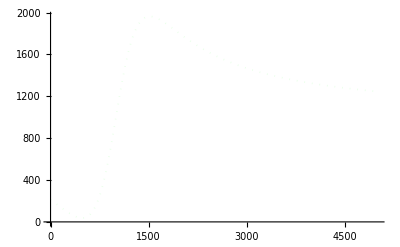

```mathematica
solPlot2=Plot[Re[sol2],{md,0,5000},PlotStyle->Directive[Lighter[Green,.9],Thickness[.003],Dotted]]
```

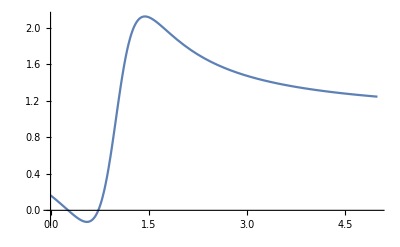

```mathematica
Plot[mQSol2,{md,0 Quantity[, "Meters"],5 Quantity[, "Meters"]}]
```

```mathematica
pointColorFunc8=Blend[blendList8,#3]&
```

Blend[blendList8,#3]&

```mathematica
ListPointPlot3D[{#[[1]]/1000,#[[2]]/1000,#[[3]]*First[#[[4]]]}&/@mirPosCouplingData11,PlotRange->{0,1},ColorFunction->pointColorFunc8,PlotLegends->Column[{
BarLegend[{colorFunc8,{0,1}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Coupling Eff.",LabelStyle->{FontFamily->"Helvetica"}](*,
SwatchLegend[{Lighter[Blue,.9]},{"Solution"}]*)}]
]
```

-Graphics3D-